## LSA2 Francesco Vassalli

### Q1

```mathematica
f[x_] := Sin[x]/x;
y[x] :=x^2
y[4]
```

y[4]

y=x^2

This sets the variable y equal to the square of the variable x.

y[x_]:=x^2

Creates the equation y=x^2

y[x] :=x^2

Does nothing

### Q2

```mathematica
ClearAll["Global`*"]
sinTable=Table[Sin[i],{i,0,6*Pi,6*Pi/100}];
sinTable+1
sinTable*10
```

{1,1+Sin[(3 π)/50],1+Sin[(3 π)/25],1+Sin[(9 π)/50],1+Sin[(6 π)/25],1+1/4 (1+√5),1+Cos[(7 π)/50],1+Cos[(2 π)/25],1+Cos[π/50],1+Cos[π/25],1+√(5/8+(√5)/8),1+Cos[(4 π)/25],1+Cos[(11 π)/50],1+Sin[(11 π)/50],1+Sin[(4 π)/25],1+1/4 (-1+√5),1+Sin[π/25],1-Sin[π/50],1-Sin[(2 π)/25],1-Sin[(7 π)/50],1-√(5/8-(√5)/8),1-Cos[(6 π)/25],1-Cos[(9 π)/50],1-Cos[(3 π)/25],1-Cos[(3 π)/50],0,1-Cos[(3 π)/50],1-Cos[(3 π)/25],1-Cos[(9 π)/50],1-Cos[(6 π)/25],1-√(5/8-(√5)/8),1-Sin[(7 π)/50],1-Sin[(2 π)/25],1-Sin[π/50],1+Sin[π/25],1+1/4 (-1+√5),1+Sin[(4 π)/25],1+Sin[(11 π)/50],1+Cos[(11 π)/50],1+Cos[(4 π)/25],1+√(5/8+(√5)/8),1+Cos[π/25],1+Cos[π/50],1+Cos[(2 π)/25],1+Cos[(7 π)/50],1+1/4 (1+√5),1+Sin[(6 π)/25],1+Sin[(9 π)/50],1+Sin[(3 π)/25],1+Sin[(3 π)/50],1,1-Sin[(3 π)/50],1-Sin[(3 π)/25],1-Sin[(9 π)/50],1-Sin[(6 π)/25],1+1/4 (-1-√5),1-Cos[(7 π)/50],1-Cos[(2 π)/25],1-Cos[π/50],1-Cos[π/25],1-√(5/8+(√5)/8),1-Cos[(4 π)/25],1-Cos[(11 π)/50],1-Sin[(11 π)/50],1-Sin[(4 π)/25],1+1/4 (1-√5),1-Sin[π/25],1+Sin[π/50],1+Sin[(2 π)/25],1+Sin[(7 π)/50],1+√(5/8-(√5)/8),1+Cos[(6 π)/25],1+Cos[(9 π)/50],1+Cos[(3 π)/25],1+Cos[(3 π)/50],2,1+Cos[(3 π)/50],1+Cos[(3 π)/25],1+Cos[(9 π)/50],1+Cos[(6 π)/25],1+√(5/8-(√5)/8),1+Sin[(7 π)/50],1+Sin[(2 π)/25],1+Sin[π/50],1-Sin[π/25],1+1/4 (1-√5),1-Sin[(4 π)/25],1-Sin[(11 π)/50],1-Cos[(11 π)/50],1-Cos[(4 π)/25],1-√(5/8+(√5)/8),1-Cos[π/25],1-Cos[π/50],1-Cos[(2 π)/25],1-Cos[(7 π)/50],1+1/4 (-1-√5),1-Sin[(6 π)/25],1-Sin[(9 π)/50],1-Sin[(3 π)/25],1-Sin[(3 π)/50],1}

{0,10 Sin[(3 π)/50],10 Sin[(3 π)/25],10 Sin[(9 π)/50],10 Sin[(6 π)/25],5/2 (1+√5),10 Cos[(7 π)/50],10 Cos[(2 π)/25],10 Cos[π/50],10 Cos[π/25],10 √(5/8+(√5)/8),10 Cos[(4 π)/25],10 Cos[(11 π)/50],10 Sin[(11 π)/50],10 Sin[(4 π)/25],5/2 (-1+√5),10 Sin[π/25],-10 Sin[π/50],-10 Sin[(2 π)/25],-10 Sin[(7 π)/50],-10 √(5/8-(√5)/8),-10 Cos[(6 π)/25],-10 Cos[(9 π)/50],-10 Cos[(3 π)/25],-10 Cos[(3 π)/50],-10,-10 Cos[(3 π)/50],-10 Cos[(3 π)/25],-10 Cos[(9 π)/50],-10 Cos[(6 π)/25],-10 √(5/8-(√5)/8),-10 Sin[(7 π)/50],-10 Sin[(2 π)/25],-10 Sin[π/50],10 Sin[π/25],5/2 (-1+√5),10 Sin[(4 π)/25],10 Sin[(11 π)/50],10 Cos[(11 π)/50],10 Cos[(4 π)/25],10 √(5/8+(√5)/8),10 Cos[π/25],10 Cos[π/50],10 Cos[(2 π)/25],10 Cos[(7 π)/50],5/2 (1+√5),10 Sin[(6 π)/25],10 Sin[(9 π)/50],10 Sin[(3 π)/25],10 Sin[(3 π)/50],0,-10 Sin[(3 π)/50],-10 Sin[(3 π)/25],-10 Sin[(9 π)/50],-10 Sin[(6 π)/25],5/2 (-1-√5),-10 Cos[(7 π)/50],-10 Cos[(2 π)/25],-10 Cos[π/50],-10 Cos[π/25],-10 √(5/8+(√5)/8),-10 Cos[(4 π)/25],-10 Cos[(11 π)/50],-10 Sin[(11 π)/50],-10 Sin[(4 π)/25],5/2 (1-√5),-10 Sin[π/25],10 Sin[π/50],10 Sin[(2 π)/25],10 Sin[(7 π)/50],10 √(5/8-(√5)/8),10 Cos[(6 π)/25],10 Cos[(9 π)/50],10 Cos[(3 π)/25],10 Cos[(3 π)/50],10,10 Cos[(3 π)/50],10 Cos[(3 π)/25],10 Cos[(9 π)/50],10 Cos[(6 π)/25],10 √(5/8-(√5)/8),10 Sin[(7 π)/50],10 Sin[(2 π)/25],10 Sin[π/50],-10 Sin[π/25],5/2 (1-√5),-10 Sin[(4 π)/25],-10 Sin[(11 π)/50],-10 Cos[(11 π)/50],-10 Cos[(4 π)/25],-10 √(5/8+(√5)/8),-10 Cos[π/25],-10 Cos[π/50],-10 Cos[(2 π)/25],-10 Cos[(7 π)/50],5/2 (-1-√5),-10 Sin[(6 π)/25],-10 Sin[(9 π)/50],-10 Sin[(3 π)/25],-10 Sin[(3 π)/50],0}

### Q3

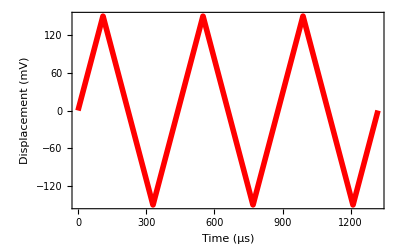

```mathematica
p=Plot[TriangleWave[{-150,150},x/440],{x,0,1320},
Frame->True,Axes->True,
LabelStyle -> {FontFamily -> "Arial", FontSize -> 13},
FrameLabel -> {"Time (μs)", "Displacement (mV)"},
FrameStyle -> Thickness[0.005],PlotStyle ->{Red, Thickness[0.01]}]
xa[x_]:=1320*x/100;
ya[y_]:=y*150;
d=ListPlot[sinTable,ScalingFunctions->{xa,ya}];
Show[p,d]
```